```mathematica
rawData=Import["c:\\Users\\kazas\\Downloads\\20190204.CSV"]
```

{{Time,Object Name,Status,Value,Units,Alert ID,Priority},{04.02.2019 14:50:24,TIC Turbo Speed,,1.7,,0,0},{04.02.2019 14:50:24,TIC Turbo Power,,7.3,,0,0},15297,{04.02.2019 16:38:02,TIC Gauge 2,5,9.9×10^9,59,0,0},{04.02.2019 16:38:02,TIC Gauge 3,5,9.9×10^9,59,0,0}}
 |  |  |  |

```mathematica
With[{r2=Repeated[_,{2}],r4=Repeated[_,{4}]},
dateInterpreter@str_:=Catch@StringReplace[str,
StartOfString~~(dd:r2)~~"."~~(MM:r2)~~"."~~(yyyy:r4)~~Whitespace~~
(hh:r2)~~":"~~(mm:r2)~~":"~~(ss:r2)~~EndOfString:>
Throw@DateObject[ToExpression/@{yyyy,MM,dd,hh,mm,ss}]
]
];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
dataset=With[{headerData=TakeDrop[rawData,1]},
With[{header=headerData⟦1,1⟧,data=headerData⟦2⟧},
makeAssoc@header/@data
]
]//Dataset;
dataset=dataset[All,{"Time"->dateInterpreter}]
```

Dataset[<>]

```mathematica
timeValueDataset=dataset[Select[#@"Object Name"=="TIC Gauge 1"&]/*SortBy[#Time&],{"Time","Value"}]
```

Dataset[<>]

```mathematica
relativeTimeValueDataset=With[{startingTime=timeValueDataset[1,"Time"]},
timeValueDataset[All,{"Time"->(#-startingTime&)}]
]
```

Dataset[<>]

```mathematica
UnitConvert[Quantity[33.,"Seconds"],"Minutes"]
```

0.55 min

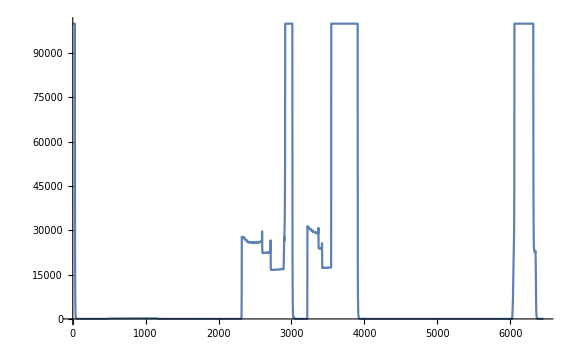

```mathematica
relativeTimeValueDataset[
ListLinePlot[#,
PlotRange->All,
ImageSize->Large,
Ticks->Automatic
]
&]
```